# Problem Set 1

## for February 09, 23.59, 2024

## Problem 1, Time delayed model with Allee effect It is well-known that individuals in many biological populations suffer from a reduced capacity to reproduce or survive when the population density (that is, size) is small. As a consequence, the population may experience extinction depending on its density. This effect is known as Allee effect [W. C. Allee et al. Principles of animal ecology (1949)]. The Allee effect can arise due to several different mechanisms, such as difficulty of finding a mate, inefficient antipredator strategies in small groups of prey (due to reduced cooperation) etc. Mechanisms that allow for the Allee effect to appear (for example reduced cooperation) are often time delayed. Denoting the population size by N, a time-delayed growth with Allee effect can be modelled as follows: Here is a time-delay parameter. Your task is to analyse how the dynamics in this model depends on the time-delay parameter . Solve Eq. (1) numerically. Integrate Eq. (1) for , up to 5. Set the remaining parameters to: , , , and (where denotes the population size at time t = 0). Assume further that during the time interval the population size was constant and equal to .

## a) Show examples of the different dynamics obtained in this model: no oscillations, damped oscillations, and stable oscillations (limit cycle).

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of NDSolveValue::ihist will be suppressed during this calculation.

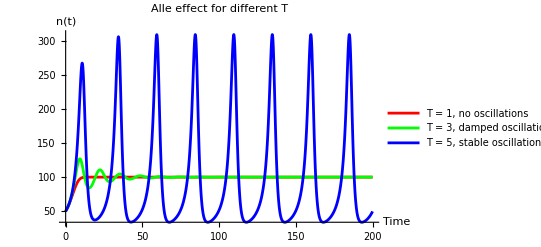

```mathematica
ClearAll["Global`*"];
A = 20;
K = 100;
r = 0.1;
initialCondition = n[0] == 50;
TValues = {1, 3, 5};
t0 = 0;
tMax = 200;

solveDifferentialEquation[T_] := NDSolveValue[
	{n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), initialCondition}, 
    n, {t, t0, tMax}
];

solutions = Table[
	solveDifferentialEquation[T], 
	{T, TValues}
];

legends = {
	"T = 1, no oscillations", 
	"T = 3, damped oscillations", 
	"T = 5, stable oscillations (limit cycles)"
};

colors = {
	Red,
	Green,
	Blue
};

Plot[Evaluate[Table[solutions[[i]][t], {i, Length[TValues]}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> legends, 
     PlotLabel -> "Alle effect for different T", 
     AxesLabel -> {"Time", "n(t)"},
     PlotStyle->colors
]
```

## b) Estimate numerically with one decimal precision the value of T at which the dynamics starts exhibiting damped oscillations.

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of NDSolveValue::ihist will be suppressed during this calculation.

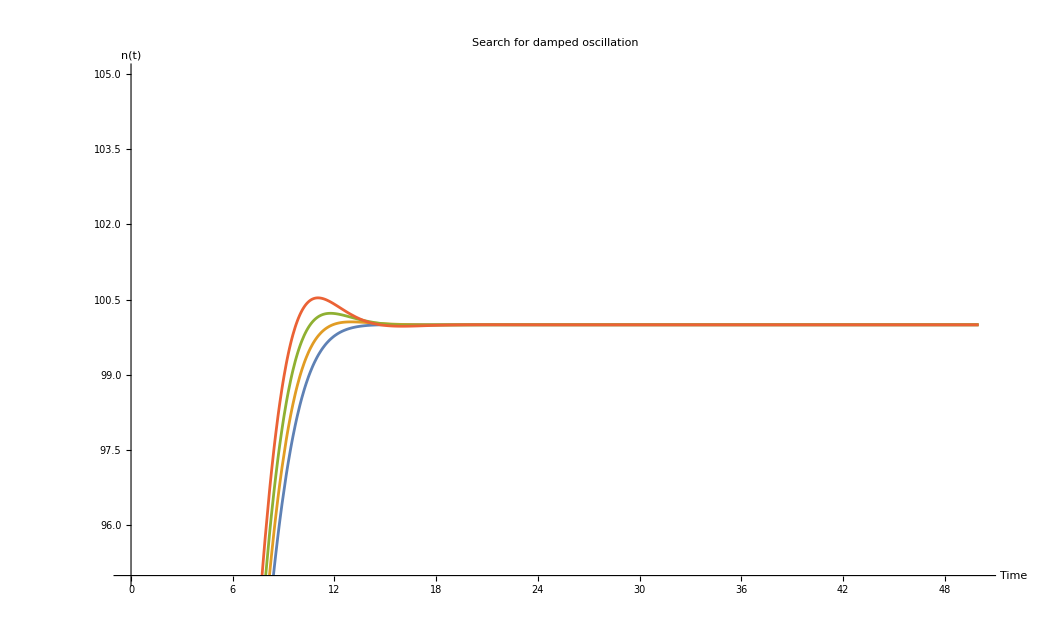

```mathematica
ClearAll["Global`*"];
A = 20;
K = 100;
r = 0.1;
initialCondition = n[0] == 50;
TValues = {1, 1.1, 1.2, 1.3};
t0 = 0;
tMax = 50;

solveDifferentialEquation[T_] := NDSolveValue[
    {n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), initialCondition}, 
    n, {t, t0, tMax}
];

solutions = Table[
    solveDifferentialEquation[T], 
    {T, TValues}
];

Plot[Evaluate[Table[solutions[[i]][t], {i, Length[TValues]}]], {t, t0, tMax},
     PlotRange -> {{t0, tMax}, {95, 105}}, 
     PlotLabel -> "Search for damped oscillation", 
     AxesLabel -> {"Time", "n(t)"}
]
```

From the plot it seem evident that the damped oscillation starts as soon as .

## c) Estimate numerically with one decimal precision the value of T (denoted by ) at which a bifurcation (Hopf bifurcation) occurs.

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of NDSolveValue::ihist will be suppressed during this calculation.

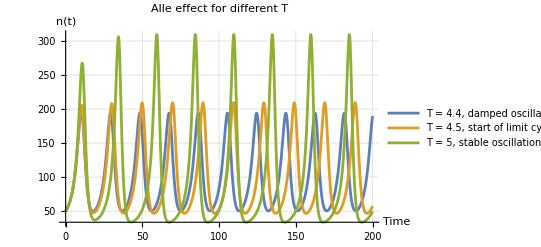

```mathematica
ClearAll["Global`*"];
A = 20;
K = 100;
r = 0.1;
initialCondition = n[0] == 50;
TValues = {4.4,4.5,5};
t0 = 0;
tMax = 200;

solveDifferentialEquation[T_] := NDSolveValue[
	{n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), initialCondition}, 
    n, {t, t0, tMax}
];

solutions = Table[
	solveDifferentialEquation[T], 
	{T, TValues}
];

legends = {
	"T = 4.4, damped oscillations", 
	"T = 4.5, start of limit cycle", 
	"T = 5, stable oscillations (limit cycles)"
};


Plot[Evaluate[Table[solutions[[i]][t], {i, Length[TValues]}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends->legends,
     PlotLabel -> "Alle effect for different T", 
     GridLines->Automatic,
     AxesLabel -> {"Time", "n(t)"}
]
```

In the plot there are shown the cases  of damped oscillation (that show stable oscillations),  the conversion from damped oscillations  to limit cycles, and  true stable oscillations, limit cycles.

## d) Use linear stability analysis to analytically compute the value of . Do this by linearising Eq. (1) around the steady state and use a perturbation that is proportional to . Compare that you obtain analytically to the estimate found in subtask c). Discuss your results.

```mathematica
ClearAll["Global`*"];
alleEq = n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1);
rhs = alleEq[[2]]

D[rhs, n[t]]
```

r n[t] (-1+n[t]/A) (1-1/100 n[t-T])

(r n[t] (1-1/100 n[t-T]))/A+r (-1+n[t]/A) (1-1/100 n[t-T])

## Problem 2, Discrete growth models [5p] Assume that the population size depends on discrete time (τ = 0,1,2,...) as follows Here, the parameters satisfy: , , and .

## a) Analytically determine the non-negative steady states (fixed points) of the model (2).

There is a trivial fixed point at , and there is a fixed point at , which can be found by setting  and solving for .

## b) Perform linear stability analysis and discuss how the linear stability of the non-negative steady states depends on the parameters.

To solve this one needs to take the derivative of the growth model which corresponds to:
 
Now insert the  and the resulting derivative is:

Now insert the  and the resulting derivative is:

In general; for non-negative fixed points it follows that if  then the fixed point is stable and if  then the fixed point is unstable. 

With the given criterion’s for  and  one can see that the stable point at  is always going to be unstable. 

The seconde stable point  If one inserts b = 1 to the solution one can see that the fixed point will always be stable for the parameters given. 
If the term   then we are in a point where the stability is going to switch from either stable to unstable or vice versa. Thus one can analyse where  and one finds that this happens when  and when  or  which is not possible due to the restrictions on the parameters. So there are infinitely many options on where a bifurcation from a stable to a unstable steady state happens. But one thing that can be said about the stability is dependent on if  leads to  (stable steady state)  or  leads to  (unstable steady state).

## c) Analytically find all conditions on the parameters (within their ranges of validity) where a bifurcation from a stable steady state to an unstable steady state occurs.

See b).

## In the following, use the parameter values: and . d) Investigate how the population size depends on time for the following values of the initial population size: and 10. For each case, use the linear stability analysis performed in task b) to approximate the population dynamics in the vicinity of the unstable steady state. [Hint: treat the initial condition as a small perturbation around the unstable steady state, and plot how this perturbation, and consequently the population size, is expected to change over time according to the linear stability analysis.] Plot this approximation together with the corresponding (exact) population dynamics obtained by iterating Eq. (2). Use log-log scale for plotting to distinguish well between the different curves.

As already hinted at in sub task b) the fixed point in question must be stable due to the fact that , and thus the derivative of the growth will remain negative for all values of . One can see the behaviour in the following plots.

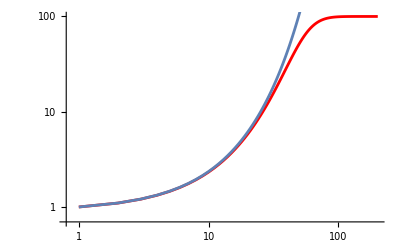

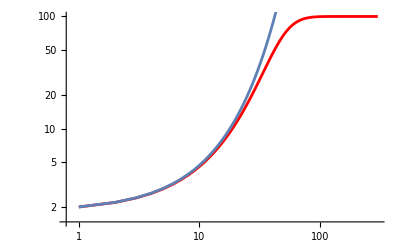

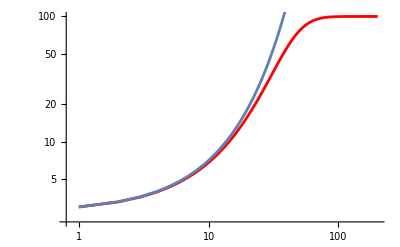

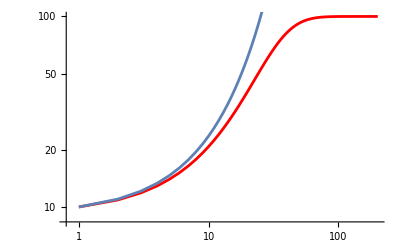

```mathematica
ClearAll["Global`*"];
b = 1;
k = 10^3;
r = 0.1;

data1 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {1}, 200];
data2 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {2}, 300];
data3 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {3}, 200];
data4 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {10}, 200];

pairedData1 = MapIndexed[{First[#2], #[[1]]} &, data1];
pairedData2 = MapIndexed[{First[#2], #[[1]]} &, data2];
pairedData3 = MapIndexed[{First[#2], #[[1]]} &, data3];
pairedData4 = MapIndexed[{First[#2], #[[1]]} &, data4];

data11 = NestList[{#[[1]]*(r+1)} &, {1}, 200];
data22 = NestList[{#[[1]]*(r+1)} &, {2}, 200];
data33 = NestList[{#[[1]]*(r+1)} &, {3}, 200];
data44 = NestList[{#[[1]]*(r+1)} &, {10}, 200];

pairedData11 = MapIndexed[{First[#2], #[[1]]} &, data11];
pairedData22 = MapIndexed[{First[#2], #[[1]]} &, data22];
pairedData33 = MapIndexed[{First[#2], #[[1]]} &, data33];
pairedData44 = MapIndexed[{First[#2], #[[1]]} &, data44];

Plot11 = ListLogLogPlot[{pairedData11},Joined->True];
Plot22 = ListLogLogPlot[{pairedData22},Joined->True];
Plot33 = ListLogLogPlot[{pairedData33},Joined->True];
Plot44 = ListLogLogPlot[{pairedData44},Joined->True];

Plot1 = ListLogLogPlot[{pairedData1}, PlotLabel -> "",Joined -> True,PlotStyle->Red];
Plot2 = ListLogLogPlot[{pairedData2}, PlotLabel -> "", Joined -> True,PlotStyle->Red];
Plot3 = ListLogLogPlot[{pairedData3}, PlotLabel -> "", Joined -> True,PlotStyle->Red];
Plot4 = ListLogLogPlot[{pairedData4}, PlotLabel -> "", Joined -> True,PlotStyle->Red];
Show[Plot1,Plot11]
Show[Plot2,Plot22]
Show[Plot3,Plot33]
Show[Plot4,Plot44]
```

## e) Discuss how well the stability analysis approximates the exact dynamics. How does the initial condition influence the approximation?

The stability analysis approximates the good in the beginning ok especially for small perturbations from the unstable fixed point. But with increasing steps they become worse, since they are not limited.

## f) Use linear stability analysis to approximate the dynamics in the vicinity of the stable steady state. Use initial population size , where is the value of the stable steady state and is an initial perturbation around . Choose and 10. Proceed as follows. Starting from an initial perturbation , approximate the dynamics until the system comes close to using the linear stability analysis around the stable steady state. Plot this approximation together with the exact dynamics, starting at . Perform the approximation for the different values of the initial perturbation . How does the initial perturbation influence the approximation?

Show::gcomb: Could not combine the graphics objects in Show[,/10].

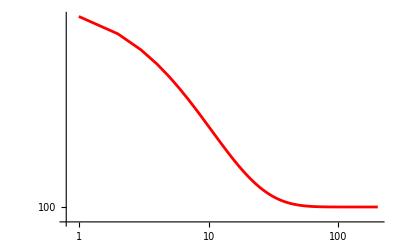
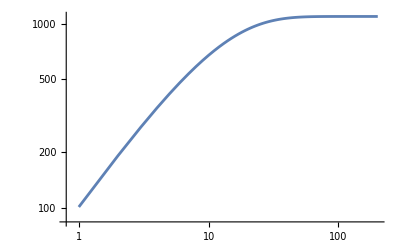
Show[-Graphics-,-Graphics-/10]

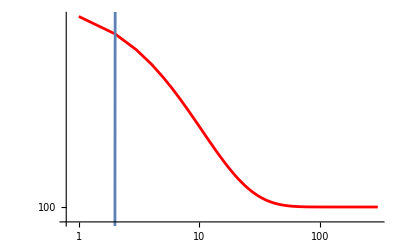

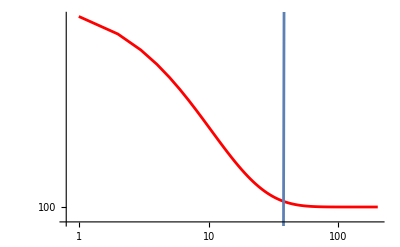

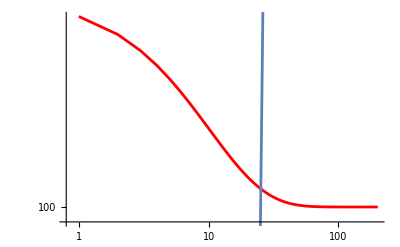

```mathematica
ClearAll["Global`*"];
b = 1;
k = 10^3;
r = 0.1;

data1 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {k*r+1}, 200];
data2 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {k*r+2}, 300];
data3 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {k*r+3}, 200];
data4 = NestList[{((r+1)*#[[1]])/(1+((#[[1]])/k)^b)} &, {k*r+10}, 200];

pairedData1 = MapIndexed[{First[#2], #[[1]]} &, data1];
pairedData2 = MapIndexed[{First[#2], #[[1]]} &, data2];
pairedData3 = MapIndexed[{First[#2], #[[1]]} &, data3];
pairedData4 = MapIndexed[{First[#2], #[[1]]} &, data4];

data11 = NestList[{k*r+(1-(b*r)/(1+r))*1} &, {k*r+1}, 200];
data22 = NestList[{k*r^(1/b)+ #[[1]]*(1-(b*r)/(1+r))} &, {2}, 200];
data33 = NestList[{#[[1]]*(r+1)} &, {3}, 200];
data44 = NestList[{#[[1]]*(r+1)} &, {10}, 200];

pairedData11 = MapIndexed[{First[#2], #[[1]]} &, data11];
pairedData22 = MapIndexed[{First[#2], #[[1]]} &, data22];
pairedData33 = MapIndexed[{First[#2], #[[1]]} &, data33];
pairedData44 = MapIndexed[{First[#2], #[[1]]} &, data44];

Plot11 = ListLogLogPlot[{pairedData11},Joined->True];
Plot22 = ListLogLogPlot[{pairedData22},Joined->True];
Plot33 = ListLogLogPlot[{pairedData33},Joined->True];
Plot44 = ListLogLogPlot[{pairedData44},Joined->True];

Plot1 = ListLogLogPlot[{pairedData1}, PlotLabel -> "",Joined -> True,PlotStyle->Red];
Plot2 = ListLogLogPlot[{pairedData2}, PlotLabel -> "", Joined -> True,PlotStyle->Red];
Plot3 = ListLogLogPlot[{pairedData3}, PlotLabel -> "", Joined -> True,PlotStyle->Red];
Plot4 = ListLogLogPlot[{pairedData4}, PlotLabel -> "", Joined -> True,PlotStyle->Red];
Show[Plot1,Plot11]
Show[Plot2,Plot22]
Show[Plot3,Plot33]
Show[Plot4,Plot44]
```

## Problem 3, A route to chaos [5p] The dynamics of a population with adults cannibalising on their offspring can be described by the Ricker map where denotes the number of adults in generation , while is related to the number of offspring produced by each adult and α is the incidence rate of cannibalism. The factor describes the probability of offspring survival to maturity. In this task you will analyse the stability of the steady states of the Ricker map as a function of the parameter for α = 0.01 and .

## a) Assume that takes the values from 1 to 30 in steps of 0.1 and plot the bifurcation diagram of η against as follows. For each value of , run the model for 300 generations and plot the last 100 values of versus the value of . The final plot should show the results for all values of tested. Describe the result.

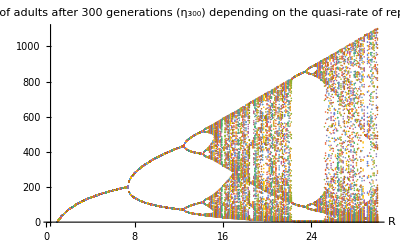

```mathematica
ClearAll["Global`*"];
MaxGeneration = 300;
η = 900;
α = 0.01;

dataPoints = Table[
	(* First data will be created using NestList and then the first 200 data points are dropped.*)
    data = Drop[NestList[R*(#)*Exp[-(α*(#))] &, η, MaxGeneration], 200];
    (* Now the data which is a list of values is changed to a list of list with two elements {{R, dataPoint1}, {R, dataPoint2}, ...} *)
    pairedData = Map[{R, #} &, data];
    {R, pairedData},
    {R, 1, 30, 0.1}];

ListPlot[dataPoints[[All, 2]], 
 AxesLabel -> {"R", ""}, 
 PlotRange -> All,
 PlotLabel->"Amount of adults after 300 generations (η_300) depending on the quasi-rate of reproduction (R)"]
```

In the plot we can see fractal behaviour, with infinite period doubling. Each point on the map corresponds to a cycle starting with a fixed point (1-point cycle) until  then a 2-point cycle start and goes over to a 4-point cycle around . This doubling goes on until  is reached where the period is infinite. If one overshoots this  the full period doubling pattern reappears in small windows of the plot ().

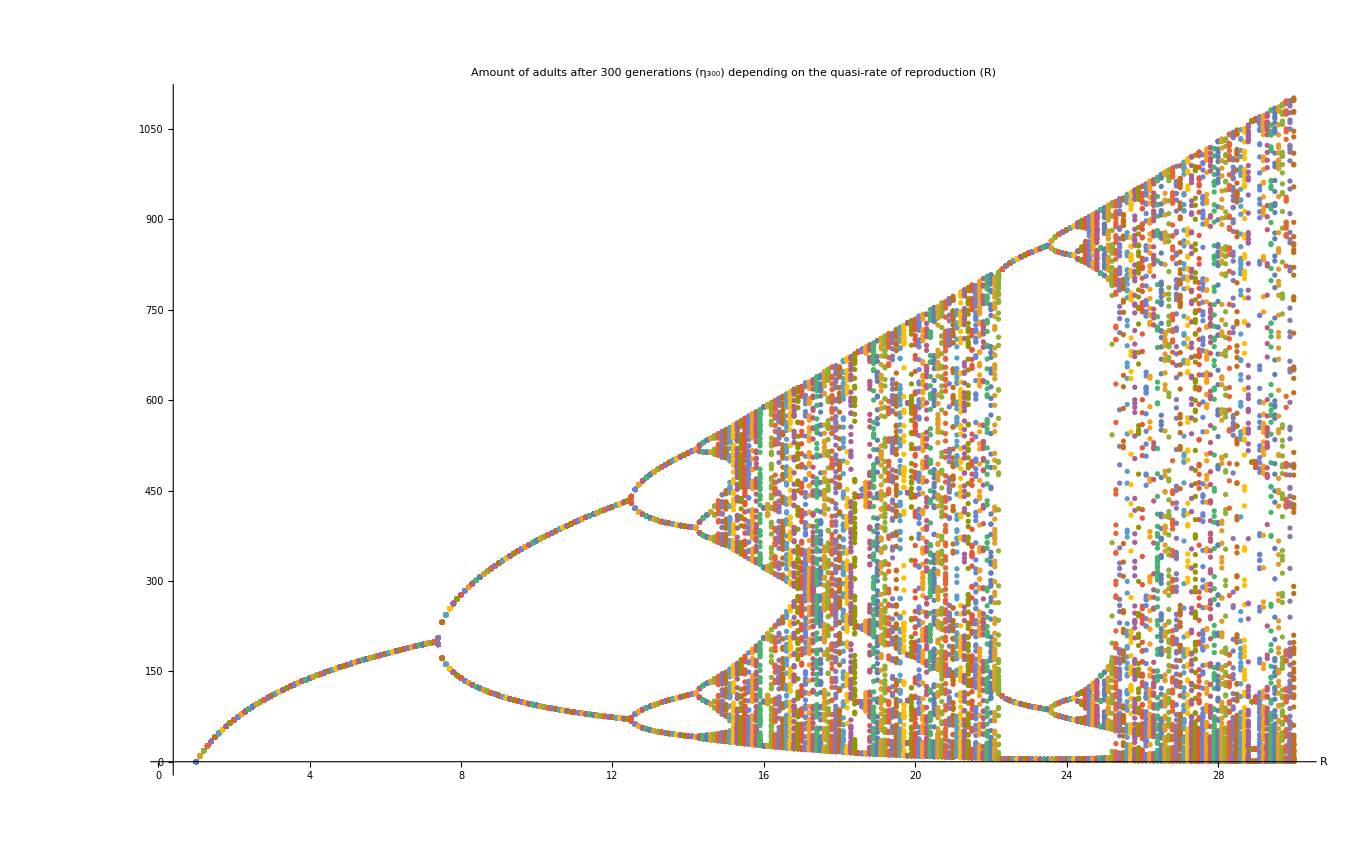

## b) Plot the population dynamics versus τ (where τ = 0, . . . , 40) for four values of . Choose four representative values of where has a stable fixed point, a 2-point cycle. a 3-point cycle, and a 4-point cycle. Describe the dynamics observed for the four values of .

I found a stable fixed point for the value of = 5, a 2-point cycle for , a 3-point cycle for  and a 5-point cycle for .

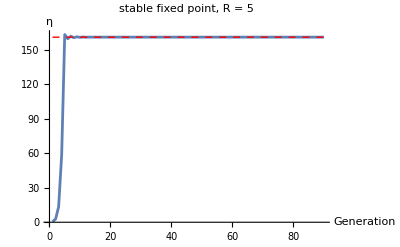

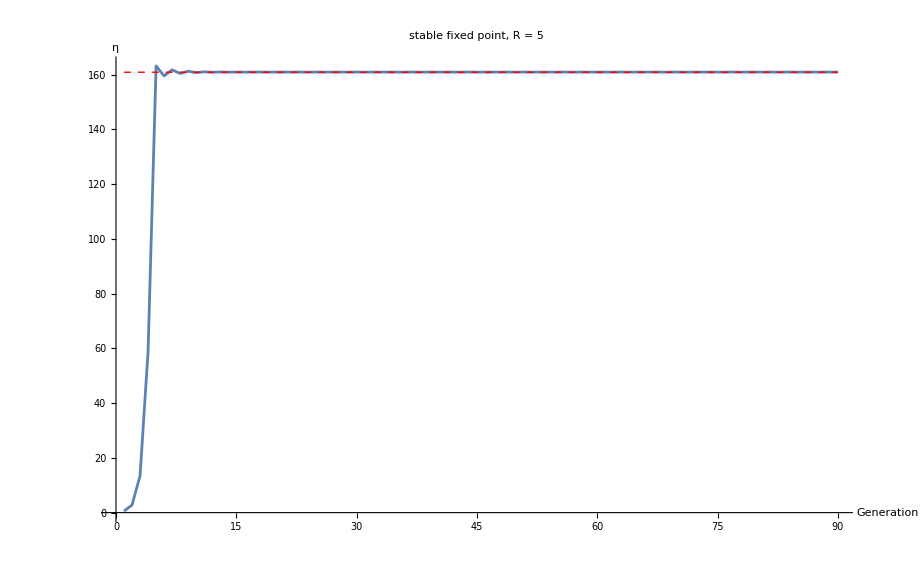

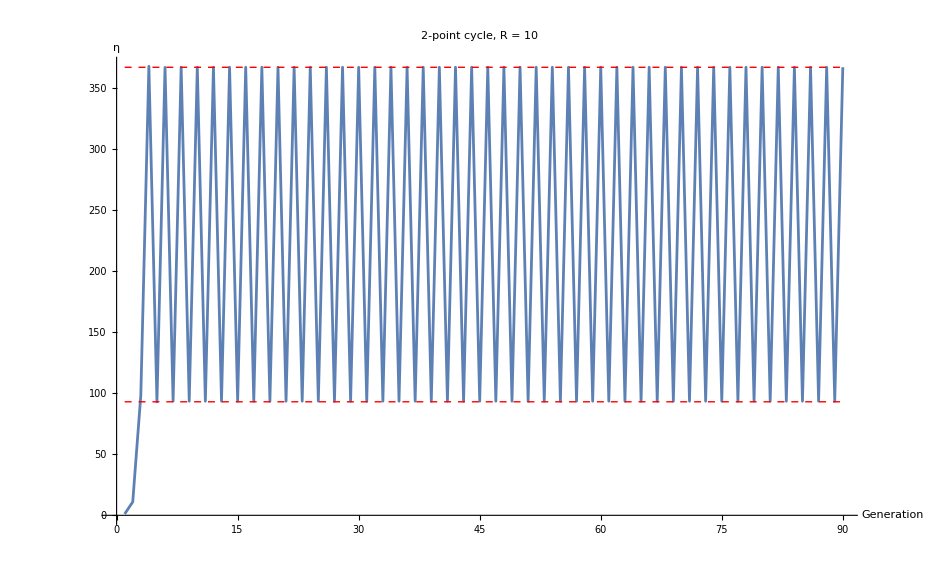

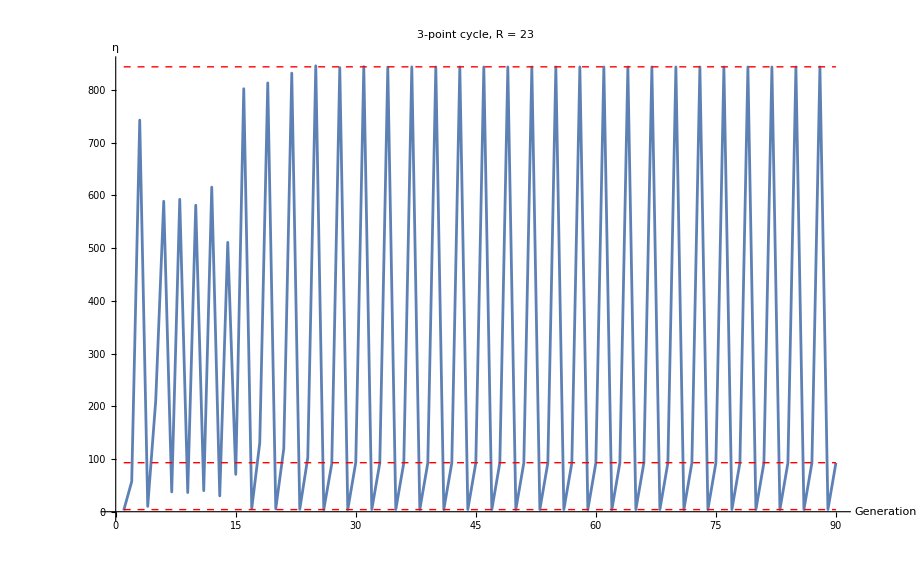

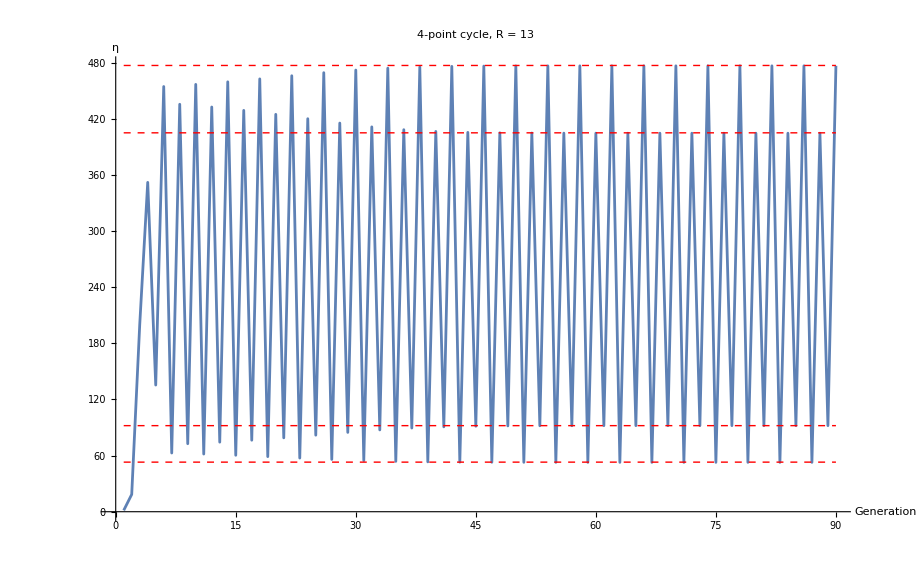

```mathematica
ClearAll["Global`*"];
η = 900;
α = 0.01;
R = 5;

dataPoints = Table[
    data = Drop[NestList[R*(#)*Exp[-(α*(#))] &, η, MaxGeneration], MaxGeneration];
    pairedData = MapIndexed[{First[#2] + MaxGeneration - Length[data], #1} &, data];
    pairedData,
    {MaxGeneration, 1, 90, 1}];

ListPlot[Flatten[dataPoints, 1], 
 AxesLabel -> {"Generation", "η"}, 
 PlotRange -> All, 
 PlotLabel -> "stable fixed point, R = 5",
 Joined -> True,
  Epilog -> {
  Red, Dashed,Line[{{1, 160.9}, {90, 160.9}}]
  }]
```

## c) Investigating the plot in subtask a), at which value of does the population dynamics bifurcate from a stable equilibrium to a stable 2-point cycle? At which value does the dynamics bifurcate to a stable 4-point cycle?

From the plot of a) it looks like that for  the bifurcation happens and goes over to a stable 2-point cycle, while the 4-point cycle appears for .

## d) By making zooms and refining the -grid, make a rough estimate of , the first parameter value where the period-doubling bifurcation has repeated an infinite number of times. Explain how you come to this estimate of .

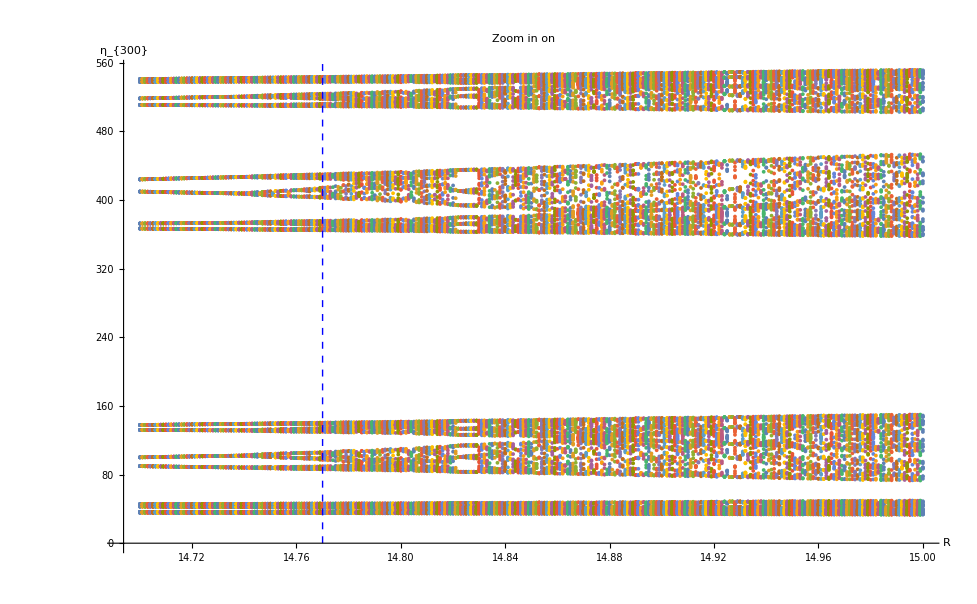

```mathematica
ClearAll["Global`*"];
MaxGeneration = 300;
η = 900;
α = 0.01;

dataPoints = Table[
	(* First data will be created using NestList and then the first 200 data points are dropped.*)
    data = Drop[NestList[R*(#)*Exp[-(α*(#))] &, η, MaxGeneration], 200];
    (* Now the data which is a list of values is changed to a list of list with two elements {{R, dataPoint1}, {R, dataPoint2}, ...} *)
    pairedData = Map[{R, #} &, data];
    {R, pairedData},
    {R, 14.7, 15, 0.001}];

ListPlot[dataPoints[[All, 2]], 
 AxesLabel -> {"R", "η_{300}"}, 
 PlotRange -> All,
 PlotLabel -> "Zoom in on ",
 Epilog -> {Blue, Dashed, Line[{{14.77, 0}, {14.77, 600}}]}
]
```

My guesstimate for the  is around . This because that is where the pockets close for the first time. When they close the period doubling has happened an infinite amount of times.